# Generating Spectra from Artificial Data

## Mercury Consortium Calculated Spectra

Create spectra from IR intensities:

```mathematica
SpectrumManifest[freq_,intensity_,broadening_]:=PDF@MixtureDistribution[intensity,NormalDistribution[#,broadening]&/@freq]
```

```mathematica
waterData=Transpose@Drop[Import["/Users/maddimarrone/Research/water data.csv","Data"],2];
```

```mathematica
waterFreqList=waterData[[1]];
```

```mathematica
waterIntensityList=waterData[[2]];
```

```mathematica
waterSpec=SpectrumManifest[waterFreqList,waterIntensityList,20];
```

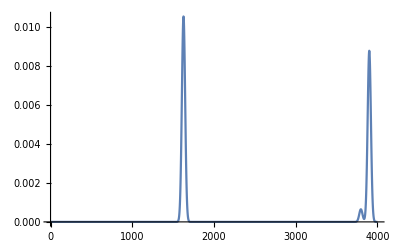

```mathematica
waterPlot=Plot[waterSpec[x],{x,0,4000},PlotRange->All]//Quiet
```

```mathematica
ethanolData=Transpose@Drop[Import["/Users/maddimarrone/Research/ethanol data.csv","Data"],2];
```

```mathematica
ethanolFreqList=ethanolData[[1]];
```

```mathematica
ethanolIntensityList=ethanolData[[2]];
```

```mathematica
ethanolSpec=SpectrumManifest[ethanolFreqList,ethanolIntensityList,20];
```

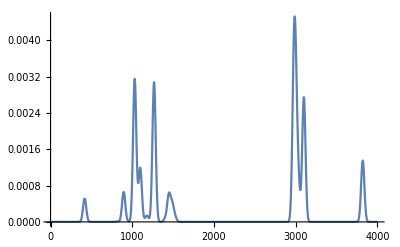

```mathematica
ethanolPlot=Plot[ethanolSpec[x],{x,0,4000},PlotRange->All]//Quiet
```

```mathematica
methanolData=Transpose@Drop[Import["/Users/maddimarrone/Research/methanol data.csv","Data"]2];
```

```mathematica
methanolFreqList=methanolData[[1]];
```

```mathematica
methanolIntensityList=methanolData[[2]];
```

```mathematica
methanolSpec=SpectrumManifest[methanolFreqList,methanolIntensityList,20];
```

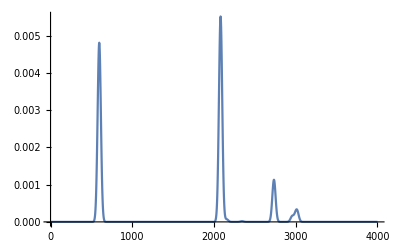

```mathematica
methanolPlot=Plot[methanolSpec[x],{x,0,4000},PlotRange->All]//Quiet
```

```mathematica
acetaldData=Transpose@Drop[Import["/Users/maddimarrone/Research/acetaldehyde data.csv","Data"]2];
```

```mathematica
acetaldFreqList=acetaldData[[1]];
```

```mathematica
acetaldIntensityList=acetaldData[[2]];
```

```mathematica
acetaldSpec=SpectrumManifest[acetaldFreqList,acetaldIntensityList,20];
```

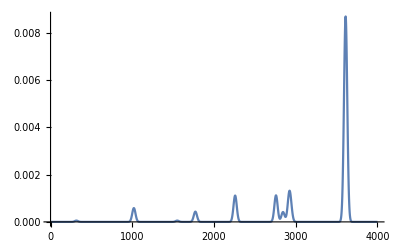

```mathematica
acetaldPlot=Plot[acetaldSpec[x],{x,0,4000},PlotRange->All]//Quiet
```

# Extrapolating Data Points

Create a function that will solve for points along the graph of pure spectra.

```mathematica
GetPoints[spectra_]:=Table[spectra[x],{x,500,4000}]//Quiet
```

```mathematica
waterPoints=GetPoints[waterSpec];
ethanolPoints=GetPoints[ethanolSpec];
methanolPoints=GetPoints[methanolSpec];
acetaldehydePoints=GetPoints[acetaldSpec];
```

```mathematica
(*normalize points to a scale of 0-1*)
```

```mathematica
specMatrix=Rescale/@{waterPoints,ethanolPoints,methanolPoints,acetaldehydePoints};
Dimensions[specMatrix]
```

{4,3501}

## Concentration Diagram for Multi-dimensional Mixtures

The stock solutions that create mixtures each have their own dimension in space. A point in space represents the concentrations of every species in the system as a separate component.

## The Volume Fraction

For our 4-component mixture, we are defining water as the origin (0,0). Ethanol, methanol, and acetaldehyde are all independent variables, water will be dependent on their sum.

```mathematica
(*visualization of the region that each independent substance creates as a mixture*)
```

```mathematica
RegionPlot3D[(e+m+a<=1),{e,0,1},{m,0,1},{a,0,1}]
```

-Graphics3D-

We can create a function that samples points from a region defined by the convex hull of the mixture.

```mathematica
(*the convex hull of our mixture*)
```

```mathematica
species={{0,0,0},{1,0,0},{0,1,0},{0,0,1}}
ConvexHullMesh[species]
```

-Graphics3D-

```mathematica
(*sampling random points from this region yields three values that add up to <1 with the remaining amount being water*)
RandomPoint[ConvexHullMesh[species]]
```

{0.0629082,0.303091,0.375857}

```mathematica
(*for the concentration matrix, want all 4 values*)
```

```mathematica
volFractions[species_List]:=With[{w=1-Total[points=RandomPoint[mixture=ConvexHullMesh[species]]]},Prepend[w]@points]
```

```mathematica
volFractions[species]
```

{0.105168,0.135245,0.309746,0.449841}

Now, we can construct our concentration “matrix” using this function.

```mathematica
concMatrix=Table[volFractions[species],{i,20}];(*a list of 20 concentration values as {water, ethanol, methanol, acetaldehyde}*)
Dimensions[concMatrix]
```

{20,4}

# Simulated Data Generation

We will evaluate the performance of various ML models using the absorbances from the pure spectra as predictor variables and the concentrations of all the mixture components as target variables. Applying a dot product between our two matrices yields a new matrix where each row is a new spectrum corresponding to a mixture of known concentrations.

```mathematica
trainMixtures=concMatrix.specMatrix;
Dimensions[trainMixtures]
```

{20,3501}

```mathematica
(*the spectrum for a mixture in this new matrix*)
```

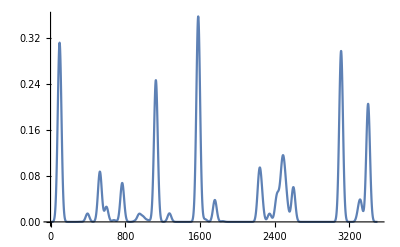

```mathematica
ListLinePlot[trainMixtures[[20]],PlotRange->All]
```